# Plotting Stuff

```mathematica
wtbs[max_,a_,b_,d_,g_,more_]:=Module[
{zetaPool,i,
zetaPool = ConstantArray[0,more];
zetaPool[[1]] = a;
For[i=2, i≤more, i++,
zetaPool[[i]] = zetaPool[[i - 1]] * (b * (1+(g * (i/max)^(d))));
];
zetaPool
]
```

```mathematica
maxFun=36;
a=0.019988028;
b=1.8373057;
d=5.0736518;
g=1.5766373;
wtbs[maxFun,a,b,d,g,maxFun+1]
```

```mathematica
{0.019988028,0.036724142542826514,0.06747383244205285,0.12397287243910995,0.22779211363609742,0.41859811633791094,0.7693914543194151,1.4146884589799624,2.6028286961337335,4.7935388053054755,8.841088104308508,16.340982812639428,30.29303997886651,56.385645908238736,105.52085922740177,198.8675188331768,378.1804113166102,727.3635351695457,1418.7040338891381,2814.869962187927,5701.092448776257,11832.086298153878,25269.12500837842,55782.83762307359,127896.20655381161,306059.28263231897,768303.5517708461,2.0334576182731814*^6,5.702654109122592*^6,1.7027682966794822*^7,5.4383450196546495*^7,1.865852496859555*^8,6.904019448552017*^8,2.764952840632921*^9,1.2022750446860813*^10,5.691654699449915*^10,2.94036039376586*^11
```

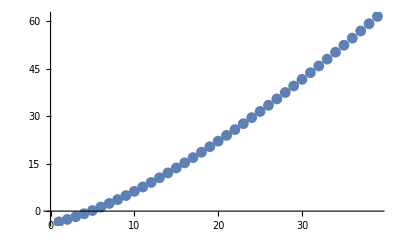

```mathematica
ListPlot[Log[wtbs[maxFun,a,b,g,d,maxFun+1]]]
```

# non-rel data

```mathematica
bsData={
{02, 8.140*10^-2, 1.953, 4.504, 1.515},
{03 , 1.596*10^-2, 1.933, 5.701, 1.573},
{04 , 2.647*10^-2, 1.938, 5.841, 1.594},
{05 , 3.238*10^-2, 1.948, 5.573, 1.523},
{06 , 4.613*10^-2, 1.941, 4.717, 1.317},
{07 , 5.976*10^-2, 1.923, 5.183, 1.442},
{08 , 6.967*10^-2, 1.936, 5.170, 1.426},
{09 , 8.321*10^-2, 1.942, 5.084, 1.408},
{10 , 9.943*10^-2, 1.945, 4.988, 1.392},
{11 , 1.696*10^-2, 1.950, 6.056, 1.469},
{12 , 2.375*10^-2, 1.932, 5.686, 1.430},
{13 , 2.239*10^-2, 1.898, 5.555, 1.413},
{14, 3.352*10^-2, 1.921, 5.419, 1.410},
{15 , 4.410*10^-2, 1.907, 5.196, 1.390},
{16 , 5.004*10^-2, 1.896, 4.962, 1.362},
{17 , 5.831*10^-2, 1.886, 4.784, 1.344},
{18 , 6.834*10^-2, 1.878, 4.654, 1.331},
{19 , 1.392*10^-2, 1.889, 6.354, 1.523},
{20 , 1.837*10^-2, 1.874, 6.109, 1.504},
{21 , 2.040*10^-2, 1.878, 6.160, 1.505},
{22 , 2.218*10^-2, 1.886, 6.247, 1.508},
{23 , 2.361*10^-2, 1.887, 6.573, 1.507},
{24 , 2.345*10^-2, 1.865, 5.348, 1.407},
{25 , 2.572*10^-2, 1.865, 5.336, 1.407},
{26 , 2.621*10^-2, 1.869, 5.301, 1.395},
{27 , 2.643*10^-2, 1.871, 5.905, 1.413},
{28 , 2.882*10^-2, 1.875, 5.935, 1.413},
{29 , 2.283*10^-2, 1.857, 5.485, 1.413},
{30 , 3.297*10^-2, 1.881, 5.817, 1.339},
{31 , 2.742*10^-2, 1.863, 5.703, 1.462},
{32 , 3.143*10^-2, 1.848, 5.290, 1.386},
{33 , 4.728*10^-2, 1.869, 5.325, 1.340},
{34, 5.087*10^-2, 1.847, 4.949, 1.533},
{35 , 5.927*10^-2, 1.861, 5.192, 1.333},
{36 , 6.804*10^-2, 1.859, 5.510, 1.370},
{37 , 1.421*10^-2, 1.856, 7.181, 1.626},
{38 , 1.808*10^-2, 1.846, 6.674, 1.553},
{39 , 1.997*10^-2, 1.841, 6.569, 1.543},
{40 , 2.184*10^-2, 1.837, 6.485, 1.535},
{41 , 2.340*10^-2, 1.835, 6.434, 1.530},
{42, 2.537*10^-2, 1.832, 6.372, 1.524},
{43  , 2.597*10^-2, 1.836, 6.453, 1.534},
{44  , 2.682*10^-2, 1.833, 6.788, 1.606},
{45 , 2.751*10^-2, 1.835, 6.883, 1.620},
{46 , 5.944*10^-2, 1.827, 5.980, 1.504},
{47, 2.438*10^-2, 1.800, 5.521, 1.423},
{48, 2.911*10^-2, 1.786, 5.334, 1.408},
{49, 2.714*10^-2, 1.799, 5.540, 1.431},
{50, 2.884*10^-2, 1.794, 5.422, 1.415},
{51, 4.481*10^-2, 1.815, 6.567, 1.605},
{52, 4.846*10^-2, 1.817, 6.247, 1.528},
{53, 5.369*10^-2, 1.810, 6.016, 1.505},
{54, 5.981*10^-2, 1.802, 5.862, 1.490},
{55, 1.177*10^-2, 1.792, 6.485, 1.510},
{56, 1.560*10^-2, 1.770, 6.152, 1.518},
{57, 1.716*10^-2, 1.764, 6.067, 1.513},
{58, 1.652*10^-2, 1.774, 6.254, 1.529},
{59, 1.696*10^-2, 1.776, 6.297, 1.533},
{60, 1.737*10^-2, 1.778, 6.563, 1.579},
{61, 1.784*10^-2, 1.780, 6.615, 1.585},
{62, 1.857*10^-2, 1.778, 5.842, 1.464},
{63, 1.876*10^-2, 1.784, 6.718, 1.596},
{64 , 1.926*10^-2, 1.782, 6.844, 1.599},
{65,1.971*10^-2, 1.784,6.898,1.604},
{66 , 2.020*10^-2, 1.788, 6.543, 1.540},
{67,2.064*10^-2, 1.785, 7.090, 1.640},
{68 , 2.106*10^-2, 1.792, 7.029, 1.638},
{69 , 2.152*10^-2, 1.794, 7.075, 1.643},
{70 , 2.200*10^-2, 1.795, 7.141, 1.652},
{71  , 2.373*10^-2, 1.790, 7.018, 1.640},
{72 , 2.511*10^-2, 1.788, 6.963, 1.636},
{73 , 2.684*10^-2, 1.784, 6.907, 1.633},
{74 , 2.814*10^-2, 1.783, 6.889, 1.633},
{75 , 2.931*10^-2, 1.782, 6.886, 1.634},
{76 , 3.075*10^-2, 1.781, 6.896, 1.637},
{77  , 3.195*10^-2, 1.780, 6.867, 1.635},
{78 , 3.173*10^-2, 1.785, 7.020, 1.654},
{79 , 3.190*10^-2, 1.791, 6.702, 1.569},
{80 , 3.546*10^-2, 1.781, 6.691, 1.604},
{81 , 3.241*10^-2, 1.794, 6.826, 1.561},
{82 , 3.867*10^-2, 1.778, 6.948, 1.656},
{83, 4.514*10^-2, 1.766, 6.158, 1.545},
{84, 4.783*10^-2, 1.763, 5.977, 1.516},
{85, 5.210*10^-2, 1.757, 5.846, 1.502},
{86,5.716*10^-2, 1.749, 5.695, 1.486}
};
```

```mathematica
alphaPlot=ListPlot[
Transpose[{bsData[[All,1]], bsData[[All,2]]}],
Frame->True,
FrameLabel->{"Nuclear Charge", "α"},
PlotMarkers->{"■"},
BaseStyle->{
FontSize->30
},
ImageSize->1500,
Prolog->{
Opacity[0.25],
Green, Rectangle[{2,-1},{4,10}], Rectangle[{10,-1},{12,10}],Rectangle[{18,-1},{20,10}],Rectangle[{36,-1},{38,10}],Rectangle[{54,-1},{56,10}],
Blue, Rectangle[{4,-1},{10,10}], Rectangle[{12,-1},{18,10}],Rectangle[{30,-1},{36,10}],Rectangle[{48,-1},{54,10}],Rectangle[{81,-1},{86,10}],
Red, Rectangle[{20,-1},{30,10}], Rectangle[{38,-1},{48,10}],Rectangle[{70,-1},{81,10}],
Yellow, Rectangle[{56,-1},{70,10}]
}
]
Export["/Users/dylan/thesis/dylan_thesis_from_ahmed_template/Figures/BS_non_rel_alpha.png",alphaPlot]
```

-Graphics-

/Users/dylan/thesis/dylan_thesis_from_ahmed_template/Figures/BS_non_rel_alpha.png

```mathematica
betaPlot=ListPlot[
Transpose[{bsData[[All,1]], bsData[[All,3]]}],
Frame->True,
FrameLabel->{"Nuclear Charge", "β"},
PlotMarkers->{"■"},
BaseStyle->FontSize->30,
ImageSize->1500,
Epilog->{
Line[{{2,-1},{2,2}}],
Line[{{4,-1},{4,2}}],
Line[{{10,-1},{10,2}}],
Line[{{12,-1},{12,2}}],
Line[{{18,-1},{18,2}}],
Line[{{20,-1},{20,2}}],
Line[{{30,-1},{30,2}}],
Line[{{36,-1},{36,2}}],
Line[{{38,-1},{38,2}}],
Line[{{48,-1},{48,2}}],
Line[{{54,-1},{54,2}}],
Line[{{56,-1},{56,2}}],
Line[{{70,-1},{70,2}}],
Line[{{80,-1},{80,2}}]
}
]
Export["/Users/dylan/thesis/dylan_thesis_from_ahmed_template/Figures/BS_non_rel_beta.png",betaPlot]
```

-Graphics-

/Users/dylan/thesis/dylan_thesis_from_ahmed_template/Figures/BS_non_rel_beta.png

```mathematica
deltaPlot=ListPlot[
Transpose[{bsData[[All,1]], bsData[[All,4]]}],
Frame->True,
FrameLabel->{"Nuclear Charge", "δ"},
PlotMarkers->{"■"},
BaseStyle->FontSize->30,
ImageSize->1500,
Epilog->{
Line[{{2,-1},{2,8}}],
Line[{{4,-1},{4,8}}],
Line[{{10,-1},{10,8}}],
Line[{{12,-1},{12,8}}],
Line[{{18,-1},{18,8}}],
Line[{{20,-1},{20,8}}],
Line[{{30,-1},{30,8}}],
Line[{{36,-1},{36,8}}],
Line[{{38,-1},{38,8}}],
Line[{{48,-1},{48,8}}],
Line[{{54,-1},{54,8}}],
Line[{{56,-1},{56,8}}],
Line[{{70,-1},{70,8}}],
Line[{{80,-1},{80,8}}]
}
]
Export["/Users/dylan/thesis/dylan_thesis_from_ahmed_template/Figures/BS_non_rel_delta.png",deltaPlot]
```

-Graphics-

/Users/dylan/thesis/dylan_thesis_from_ahmed_template/Figures/BS_non_rel_delta.png

```mathematica
gammaPlot=ListPlot[
Transpose[{bsData[[All,1]], bsData[[All,5]]}],
Frame->True,
FrameLabel->{"Nuclear Charge", "γ"},
PlotMarkers->{"■"},
BaseStyle->FontSize->30,
ImageSize->1500,
Epilog->{
Line[{{2,-1},{2,8}}],
Line[{{4,-1},{4,8}}],
Line[{{10,-1},{10,8}}],
Line[{{12,-1},{12,8}}],
Line[{{18,-1},{18,8}}],
Line[{{20,-1},{20,8}}],
Line[{{30,-1},{30,8}}],
Line[{{36,-1},{36,8}}],
Line[{{38,-1},{38,8}}],
Line[{{48,-1},{48,8}}],
Line[{{54,-1},{54,8}}],
Line[{{56,-1},{56,8}}],
Line[{{70,-1},{70,8}}],
Line[{{80,-1},{80,8}}]
}
]
Export["/Users/dylan/thesis/dylan_thesis_from_ahmed_template/Figures/BS_non_rel_gamma.png",gammaPlot]
```

-Graphics-

/Users/dylan/thesis/dylan_thesis_from_ahmed_template/Figures/BS_non_rel_gamma.png